## Prior on localization n1, n2

### Inverse - gamma distribution

```mathematica
(*interval = {0.01, 100};
α=0.001;
β=nScale * (α+1);
(*β=0.18422522996251992;*)
mode = β/(α+1);


p[n_]:=β^α/Gamma[α] n^(-α-1)Exp[-β/n];
Plot[p[n],{n,0, 10}, PlotRange->All]
(p/@interval)/p[mode]//N
Print["Mode = ", β/(α+1)];
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)*)
```

### Gamma distribution

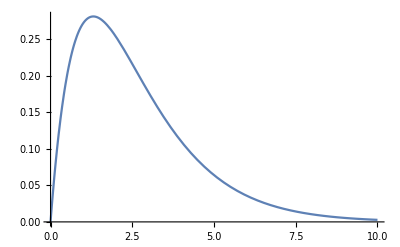

3.55873 interval

θ = 1.30918

Mode = 1.30918

ns = {10,30,100,1000} P(ns) = {0.00280999,1.95541×10^-9,3.91794×10^-32,1.08788740243069×10^-329}

```mathematica
rightBorder=10;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[n_]:=1/(Gamma[k] θ^k)n^(k-1)Exp[- n/θ];
cdf[n_]:=1-Gamma[k,n/theta]/Gamma[k]
Plot[p[n],{n,0, rightBorder}, PlotRange->All]
(p/@interval)/p[mode]//N
Print["θ = ", θ];
Print["Mode = ", mode];
ns={10, 30,100,1000};
Print["ns = ",ns, " P(ns) = ", p[ns]//N];
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)
```

## Diffusivity prior

### Gamma distribution

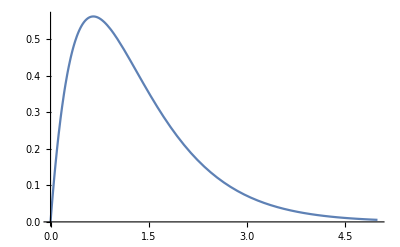

8.89682

θ = 0.654591

Mode = 0.654591

ds = {10,100,1000} P(ds) = {5.41341×10^-6,1.05239×10^-64,8.11387929413584×10^-661}

```mathematica
rightBorder=5;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[d_]:=1/(Gamma[k] θ^k)d^(k-1)Exp[- d/θ];
Plot[p[d],{d,0, rightBorder}, PlotRange->All]
(p/@rightBorder)/p[mode]//N
Print["θ = ", θ];
Print["Mode = ", mode];
ds={10,100,1000};
Print["ds = ",ds, " P(ds) = ", p[ds]//N];
(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)
```

## Link strength

### Gamma distribution for link strength

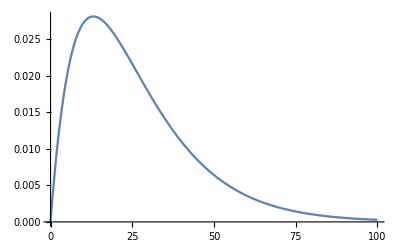

0.01

1.39429×10^-31

n12s = {10,100,1000} P(n12s) = {0.0271813,0.000280999,3.91794×10^-33}

```mathematica
rightBorder=100;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[n12_]:=1/(Gamma[k] θ^k)n12^(k-1)Exp[- n12/θ];
Plot[p[n12],{n12,0, rightBorder}, PlotRange->All]

(p[rightBorder])/p[mode]
(p[10^3])/p[mode]
n12s={10,100,1000};
Print["n12s = ",n12s, " P(n12s) = ", p[n12s]//N];
(*Print["Var=", α/(α-1) θ^2]*)
```

## Interaction angle

### Normal distribution

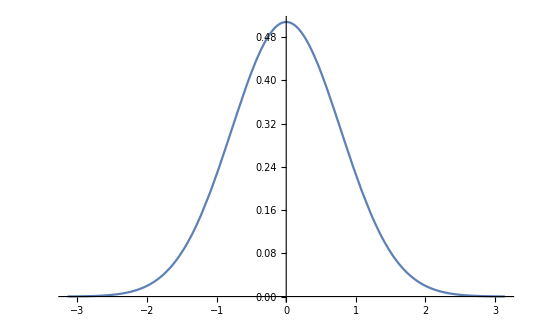

```mathematica
μ=0;
σ=π/4;

p[α_]:=1/(√(2 π σ^2))Exp[- (α-μ)^2/(2 σ^2)];
Plot[p[α],{α,-π, π}, PlotRange->All]
(*(p/@interval)/p[mode]//N
Print["θ = ", θ];
Print["Mode = ", mode];
ns={10,100,1000};
Print["ns = ",ns, " P(ns) = ", p[ns]//N];
*)(*LogLinearPlot[p[n], {n, 10^-6, 10^3}, PlotRange->All]
Plot[p[n], {n, 0, 0.5}, PlotRange->All]*)
```

## Link length for the free Hookean dumbbell model

### Gamma distribution

```mathematica
rightBorder=10;
τ=1/100;
root=FindRoot[z Exp[1-z]-τ,{z,10}];
θ=rightBorder/z/.root;
k=2;
mode=(k-1)θ;

p[L0_]:=1/(Gamma[k] θ^k)L0^(k-1)Exp[- L0/θ];
Plot[p[L0],{L0,0, rightBorder}, PlotRange->All]

(p[rightBorder])/p[mode]
(p[10^3])/p[mode]
L0s={10,100,1000};
Print["L0s = ",L0s, " P(L0s) = ", p[L0s]//N];
(*Print["Var=", α/(α-1) θ^2]*)
```

-Graphics-

0.01

1.39429×10^-31

n12s = {10,100,1000} P(n12s) = {0.0271813,0.000280999,3.91794×10^-33}